## Brian — PS 5 — 2025-02-04 — Solution

## Exercises from EIWL3 Section 14

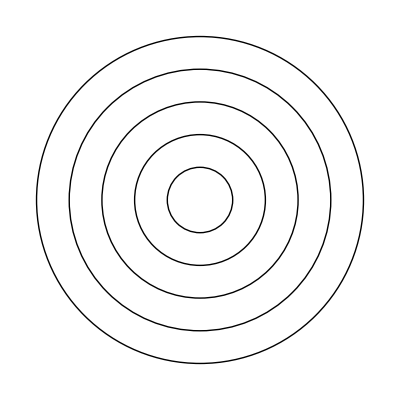

```mathematica
(* 14.1 *) Graphics[Table[Circle[{0,0},r],{r,1,5}]]
```

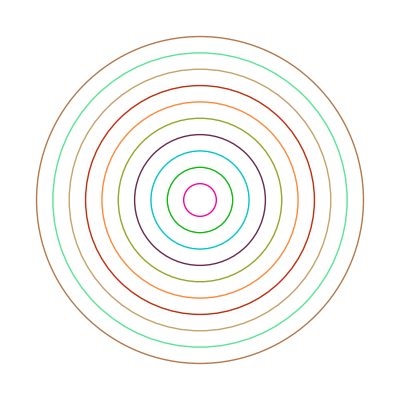

```mathematica
(* 14.2 *) Graphics[Table[Style[Circle[{0,0},r],RandomColor[]],{r,1,10}]]
```

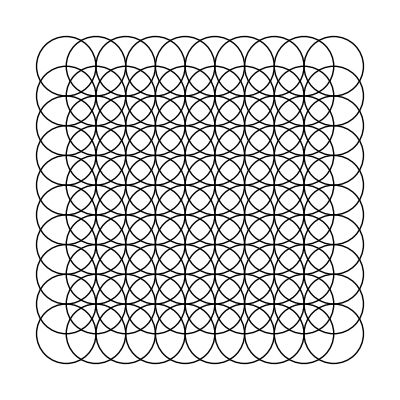

```mathematica
(* 14.3 *) Graphics[Table[Circle[{i,j}],{i,1,10},{j,1,10}]]
```

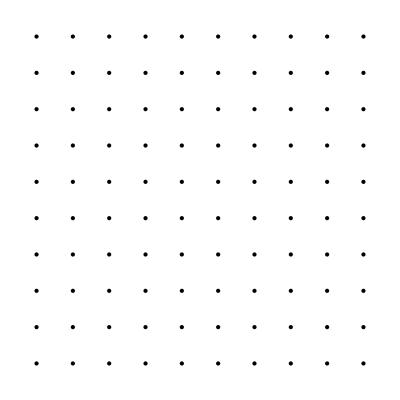

```mathematica
(* 14.4 *) Graphics[Table[Point[{x,y}],{x,1,10},{y,1,10}]]
```

```mathematica
(* 14.5 *) Manipulate[
Graphics[Table[Circle[{0,0},radius],{radius,1,count}]],
{count, 1,20}
]
```

```mathematica
(* 14.6 *) Graphics3D[Sphere[RandomInteger[150,{50,3}]]]
```

-Graphics3D-

```mathematica
(* 14.7 *) Graphics3D[Table[
Style[Sphere[{x,y,z},1/2],RGBColor[x/10,y/10,z/10]],
{x,0,10},{y,0,10},{z,0,10}]]
```

-Graphics3D-

```mathematica
(* 14.8 *) Manipulate[
Graphics[
Table[Circle[{t x,0},x],{x,1,10}]
],
{t,-2,2}
]
```

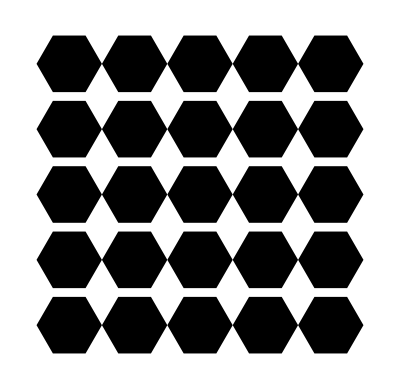

```mathematica
(* 14.9 *) Graphics[
Table[
RegularPolygon[{x,y},1/2,6],
{x,1,5},{y,1,5}]
]
```

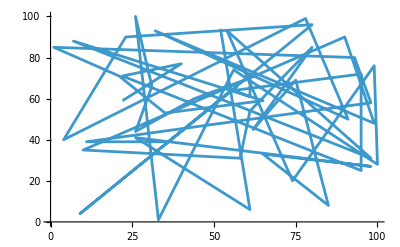

```mathematica
(* 14.10 *) ListLinePlot[RandomInteger[100,{50,2}]]
```

```mathematica
(* 14.11 *) Manipulate[
Graphics3D[{
Style[Icosahedron[{0,0},edgeLength],Opacity[0.5]],
Style[Dodecahedron[{0,0},1],Opacity[0.5]]
}],
{edgeLength,1,2}
]
```

## Exercises from EIWL3 Section 17

```mathematica
(* 17.1 *) UnitConvert[Quantity[4.5, "Pounds"],"Kilograms"]
```

2.04117 kg

```mathematica
(* 17.2 *) UnitConvert[Quantity[60.25, ("Miles")/("Hours")],"KilometersPerHour"]
```

96.963 km/h

```mathematica
(* 17.3 *)UnitConvert[ Entity["Building","EiffelTower::5h9w8"]["Height"],"Miles"]
```

0.205052 mi

```mathematica
(* 17.4 *) Entity["Mountain","MountEverest"]["Elevation"]/Entity["Building","EiffelTower::5h9w8"]["Height"]
```

26.8147

```mathematica
(* 17.5 *) Entity["Planet","Earth"]["Mass"]/Entity["PlanetaryMoon","Moon"]["Mass"]
```

81.3

```mathematica
(* 17.6 *)Quantity[, "Yen"]/Quantity[, "USDollars"]
```

0.00643845

```mathematica
(* 17.7 *) UnitConvert[Quantity[35, "Ounces"]+Quantity[0.25, "ShortTons"]+Quantity[45, "Pounds"]+Quantity[9, "Stones"],"Kilograms"]
```

305.353 kg

```mathematica
(* 17.8 *) UnitConvert[EntityClass["Planet",All]["DistanceFromEarth"],"LightMinutes"]
```

{11.7123 light minutes,4.09907 light minutes,0. light minutes,5.84529 light minutes,38.2831 light minutes,86.895 light minutes,161.413 light minutes,254.696 light minutes}

```mathematica
(* 17.9 *) Rotate["hello",180 °,{0,0}]
```

hello

```mathematica
(* 17.10 *) Table[
Rotate[Style["A",100],angle,{0,0}],
{angle, 0°,360°, 30°}
]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A}

```mathematica
(* 17.11 *) Manipulate[
Rotate[Entity["TaxonomicSpecies","FelisCatus::ddvt3"]["Image"],angle,{0,0}],
{angle, 0°,180°}
]
```

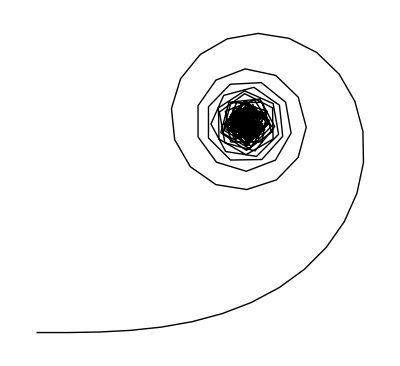

```mathematica
(* 17.12 *) Graphics[Line[AnglePath[Range[0,180]°]]]
```

```mathematica
(* 17.13 *) Manipulate[
Graphics[Line[AnglePath[Table[value °,100]]]],
{value,0,360}
]
```

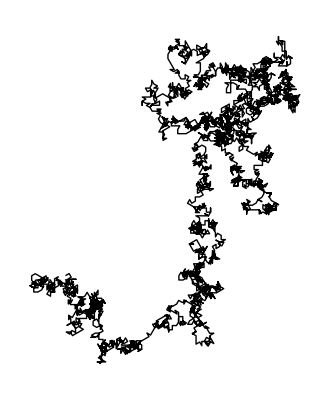

```mathematica
(* 17.14 *) Graphics[Line[AnglePath[IntegerDigits[2^10000]30°]]]
```